```mathematica
(* The list of prime factors of n *)
PrimeFactors[n_Integer]:=Flatten[Take[Transpose[FactorInteger[n]],1]];

(* The index [\Gamma:\Gamma_0(n)];*)

GG0Index[n_Integer]:=
Module[{l,s,i},
l=PrimeFactors[n];
s=n;
For[i=1,i<=Length[l],i++,
s*=1+1/l[[i]];
];
Return[s];
];
(* The number of order-2 and order-3 cone points;*)
(*Note that the number of ideal triangles in a $\Gamma_0(n)$--special triangle is (GG0Index[n]-v3[n])/3;*)
(*  which is also an upperbound for the iterates *)
v2[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,4]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],4];

If[r==3,Return[0],If[r==1,s*=2]];
];
Return[s];
];
v3[n_Integer]:=
Module[{l,s,i,r},
If[Mod[n,9]==0,Return[0]];
l=PrimeFactors[n];
s=1;

For[i=1,i<=Length[l],i++,

r=Mod[l[[i]],3];

If[r==2,Return[0],If[r==1,s*=2]];
];
Return[s];
];
(* Totient summatory function *)
Summatory[m_Integer]:=Sum[EulerPhi[i],{i,1,m}];
SqStartSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=Floor[Sqrt[n]];

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];
```

```mathematica
ZeroStartSpPoly[n_Integer]:=
Module[{t,iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,v2count=0,v3count=0,v2value,v3value},
iterateMax=(GG0Index[n]-v3[n])/3;
t=1;

v2value=v2[n];
v3value=v3[n];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
For[j=1,j<Length[vw],j++,
If[vb[[j]]!=-4,Continue[]];
(* Check if even *)
If[v2count<v2value,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-2];v2count++;Continue[]]];
(* Check if odd *)
If[v3count<v3value,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,n]==0,vb=ReplacePart[vb,j->-3];v3count++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],n]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
Break[]
];

mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{vw,vb}];
];
```

```mathematica
l4143A=ZeroStartSpPoly[41*43];
```

```mathematica
l4143B=SqStartSpPoly[41*43];
```

Complete at n = 1763

```mathematica
Max[l4143A[[1]]]
```

```mathematica
Floor[Sqrt[4/3]Sqrt[41*43]]
```

48

```mathematica
l101and103A=SqStartSpPoly[101*103];
```

Complete at n = 10403

```mathematica
Print["43 appears ", Count[l4143B[[1]],43]," times"];
Print["103 appears ", Count[l101and103A[[1]],103]," times"];
```

43 appears 41 times

103 appears 101 times

```mathematica
p=11;q=13;l=SqStartSpPoly[p*q][[1]]
```

{1,13,12,11,10,9,8,7,13,6,11,5,9,13,4,11,7,10,13,3,11,8,13,5,12,7,9,11,13,2,13,11,9,7,12,5,13,8,11,3,13,10,7,11,4,13,9,5,11,6,13,7,8,9,10,11,1}

```mathematica
p=11;q=13;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=17;q=19;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=29;q=31;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=2;q=31;l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
p=41;q=43;
Print["At n = ",p,"*",q,", we see ",q," appears ",  Count[l4143B[[1]],43]," times"];
p=101;q=103;
Print["At n = ",p,"*",q,", we see ",q," appears ",  Count[l101and103A[[1]],103]," times"];
```

At n = 11*13, we see 13 appears 11 times

At n = 17*19, we see 19 appears 17 times

At n = 29*31, we see 31 appears 29 times

At n = 2*31, we see 31 appears 2 times

At n = 41*43, we see 43 appears 41 times

At n = 101*103, we see 103 appears 101 times

```mathematica
Count
```

```mathematica
Max[l101and103A[[1]]]
```

117

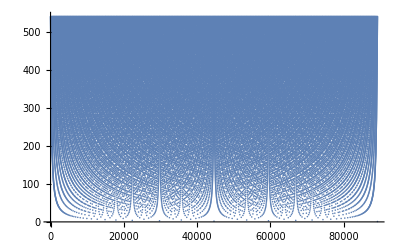

```mathematica
ListPlot[Denominator[FareySequence[p]]]
```

```mathematica
l4143A[[1]]==l4143B[[1]]
```

True

```mathematica
Count[l4143B[[2]],41]
```

```mathematica
TwinP={3,5,5,7,11,13,17,19,29,31,41,43,59,61,71,73,101,103,107,109,137,139,149,151,179,181,191,193,197,199,227,229,239,241,269,271,281,283,311,313,347,349,419,421,431,433,461,463,521,523,569,571,599,601,617,619};
```

```mathematica
For[i=1,i<=Length[TwinP]/2,i++,
p=TwinP[[2i-1]];q=TwinP[[2i]];
l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
Print["The max denominator = ",Max[l]];
Print["Floor[Sqrt[4/3 pq]] = ",Floor[Sqrt[4/3 p q]]];
];
```

At n = 3*5, we see 5 appears 3 times

The max denominator = 5

Floor[Sqrt[4/3 pq]] = 4

At n = 5*7, we see 7 appears 5 times

The max denominator = 7

Floor[Sqrt[4/3 pq]] = 6

At n = 11*13, we see 13 appears 11 times

The max denominator = 13

Floor[Sqrt[4/3 pq]] = 13

At n = 17*19, we see 19 appears 17 times

The max denominator = 20

Floor[Sqrt[4/3 pq]] = 20

At n = 29*31, we see 31 appears 29 times

The max denominator = 33

Floor[Sqrt[4/3 pq]] = 34

At n = 41*43, we see 43 appears 41 times

The max denominator = 47

Floor[Sqrt[4/3 pq]] = 48

At n = 59*61, we see 61 appears 59 times

The max denominator = 68

Floor[Sqrt[4/3 pq]] = 69

At n = 71*73, we see 73 appears 71 times

The max denominator = 81

Floor[Sqrt[4/3 pq]] = 83

At n = 101*103, we see 103 appears 101 times

The max denominator = 117

Floor[Sqrt[4/3 pq]] = 117

At n = 107*109, we see 109 appears 107 times

The max denominator = 123

Floor[Sqrt[4/3 pq]] = 124

```mathematica
For[i=2,i<=2,i++,
p=TwinP[[2i-1]];q=TwinP[[2i]];
l=SqStartSpPoly[p*q][[1]];
Print["At n = ",p,"*",q,", we see ",q," appears ", Count[l,q]," times"];
Print["The max denominator = ",Max[l]];
Print["Floor[Sqrt[4/3 pq]] = ",Floor[Sqrt[4/3 p q]]];
];
l
```

At n = 5*7, we see 7 appears 5 times

The max denominator = 7

Floor[Sqrt[4/3 pq]] = 6

{1,7,6,5,4,7,3,5,7,2,7,5,3,7,4,5,1}

```mathematica
l
```

{1,5,4,3,5,2,5,3,1}